# Hubbard Chain Exact Diagonalization

```mathematica
sites=2;sites2=2 sites;states=2^sites2;
```

## Read in the operators

Here we have that spin creation operators for a site are consecutive, with up first and down second

```mathematica
c=Array[0,{sites2,states,states}];
cdag=Array[0,{sites2,states,states}];
Table[c[[i+1,;;,;;]]=ArrayReshape[ReadList["~/Libraries/NEdyson/ED/hybfermion/build/c_"<>ToString[i]<>".dat",Number],{states,states}],{i,0,sites2-1}];
Table[cdag[[i+1,;;,;;]]=ArrayReshape[ReadList["~/Libraries/NEdyson/ED/hybfermion/build/cdag_"<>ToString[i]<>".dat",Number],{states,states}],{i,0,sites2-1}];
IM=IdentityMatrix[states];
```

## Define the Hamiltonian

```mathematica
datadir="~/Libraries/NEdysondata/";t=1;U=2;μ=0;β=20;ϵ={-1,1};B=0;H=-t (cdag[[1]].c[[3]]+cdag[[2]].c[[4]])-t Sum[cdag[[i*2]].c[[(i+1)*2]]+cdag[[i*2-1]].c[[(i+1)*2-1]]+cdag[[i*2]].c[[(i-1)*2]]+cdag[[i*2-1]].c[[(i-1)*2-1]],{i,2,sites-1}]-t(cdag[[2sites]].c[[2(sites-1)]]+cdag[[2sites-1]].c[[2(sites-1)-1]])+U Sum[(cdag[[2i -1]].c[[2i -1]]-1/2 IM).(cdag[[2 i]].c[[2 i]]-1/2 IM),{i,1,sites}]-μ Sum[cdag[[2i-1]].c[[2i-1]]+cdag[[2 i]].c[[2 i]],{i,1,sites}]+Sum[ϵ[[i]](cdag[[2i-1]].c[[2i-1]]+cdag[[2 i]].c[[2 i]]),{i,1,sites}]+B Sum[cdag[[i*2]].c[[i*2]]-cdag[[i*2-1]].c[[i*2-1]],{i,1,sites}];
Z=N[Tr[MatrixExp[-β H]]];
HEigVals =Eigensystem[H][[1]];
HEigVecs = Map[Normalize,Eigensystem[H][[2]]];
Print["Check if the Hamiltonian is Diagonalizable: "<>ToString[DiagonalizableMatrixQ[H]]<>" Max err: "]
Max[N[H-Transpose[HEigVecs].DiagonalMatrix[HEigVals].HEigVecs]]
cdagTrans=Table[HEigVecs.cdag[[i]].Transpose[HEigVecs],{i,1,sites2}];
cTrans=Table[HEigVecs.c[[i]].Transpose[HEigVecs],{i,1,sites2}];
```

Check if the Hamiltonian is Diagonalizable: True Max err:

4.44089×10^-16

## Make Matsubara Functions

```mathematica
ReadFile=OpenRead[datadir<>"/G_GM.dat"];
Params=Table[Read[ReadFile,Number],{i,1,6}];
GMNEdyson=Table[Table[Read[ReadFile,Number],{i,1,2*Params[[3]]^2}],{t,1,Params[[2]]+1}];
GM=-Table[Table[Table[1/Z Tr[DiagonalMatrix[Exp[(-β+τ)HEigVals]].cTrans[[i]].DiagonalMatrix[Exp[-τ HEigVals]].cdagTrans[[j]]],{τ,0,β,β/100}],{i,1,sites2,2}],{j,1,sites2,2}];
(*GM=-Table[Table[Table[1/Z Tr[MatrixExp[(-β+τ)H].c[[i]].MatrixExp[-τ H].cdag[[j]]],{τ,0,β,β/100}],{i,1,sites2,2}],{j,1,sites2,2}];*)
```

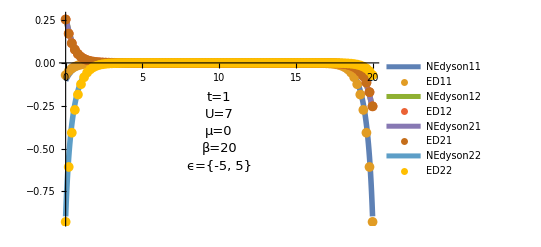

```mathematica
MPlot=ListPlot[Flatten[Table[{Transpose[{Range[0,β+β/(2*Params[[2]]),β/Params[[2]]],GMNEdyson[[;;,2i-1]]}],Transpose[{Range[0,β,β/100],GM[[Quotient[i+1,sites],Mod[i-1,sites]+1,;;]]}]},{i,1,sites*sites}],1],PlotRange->Full,Joined->Flatten[Table[{True, False},{i,1,sites*sites}]],PlotRange->Full,Joined->Flatten[Table[{True, False},{i,1,sites*sites}]],PlotStyle->{Thickness[0.01]},PlotMarkers->Flatten[Table[{None,Style[•,10]},{i,1,sites,sites}]],PlotLegends->Flatten[Table[{"NEdyson"<>ToString[Quotient[i+1,sites]]<>ToString[Mod[i-1,sites]+1],"ED"<>ToString[Quotient[i+1,sites]]<>ToString[Mod[i-1,sites]+1]},{i,1,sites*sites}]],Epilog->{Text[Style["t="<>ToString[t],13],{10,-0.2}],Text[Style["U="<>ToString[U],13],{10,-0.3}],Text[Style["μ="<>ToString[μ],13],{10,-0.4}],Text[Style["β="<>ToString[β],13],{10,-0.5}],Text[Style["ϵ="<>ToString[ϵ],13],{10,-0.6}]}]
```

```mathematica
Export[ToString[U]<>"Mat.eps",MPlot]
```

7Mat.eps

## Retarded

```mathematica
ReadFile=OpenRead[datadir<>"/G_GR.dat"];
Params=Table[Read[ReadFile,Number],{i,1,6}];
GRNEdyson =Table[Table[0,{j,1,2 Params[[3]]^2}],{i,1,Params[[1]]+1}];
Table[Table[GRNEdyson[[t,i]]=Read[ReadFile,Number],{i,1,2 Params[[3]]^2}];Table[Read[ReadFile,Number],{tp,1,2 Params[[3]]^2*(t-1)}];,{t,1,Params[[1]]+1}];
```

```mathematica
GLf1D[t_,i_,j_]:=I/Z Tr[DiagonalMatrix[Exp[-(β+I t)HEigVals]].cdagTrans[[j]].DiagonalMatrix[Exp[(I t)HEigVals]].cTrans[[i]]];
GGf1D[t_,i_,j_]:=-I/Z Tr[DiagonalMatrix[Exp[-(β-I t)HEigVals]].cTrans[[i]].DiagonalMatrix[Exp[(-I t )HEigVals]].cdagTrans[[j]]];
GRf1D[t_,i_,j_]:= GGf1D[t,i,j]-GLf1D[t,i,j];
```

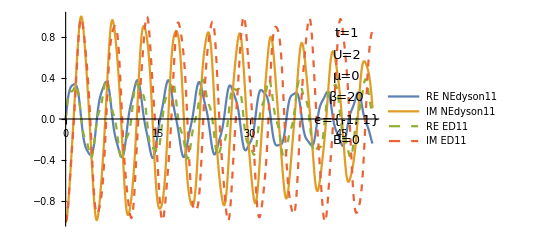
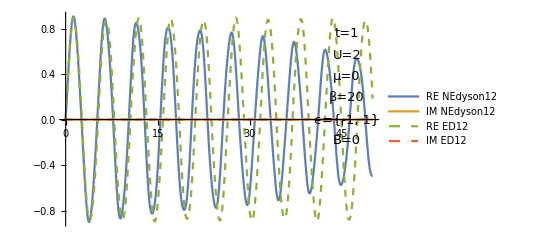
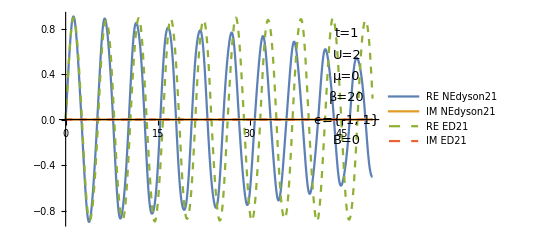
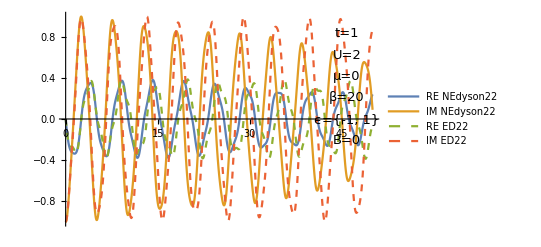

```mathematica
GRPlots=ListPlot[
{Transpose[{Range[0,Params[[1]]*Params[[4]]+10^-10,Params[[4]]],
GRNEdyson[[;;,2*sites*(#[[1]]-1)+2*(#[[2]]-1)+1]]}],
Transpose[{Range[0,Params[[1]]*Params[[4]]+10^-10,Params[[4]]],
GRNEdyson[[;;,2*sites*(#[[1]]-1)+2*(#[[2]]-1)+2]]}],Transpose[{Range[0,Params[[1]]*Params[[4]],Params[[1]]*Params[[4]]/500],
Re[Function[{t},GRf1D[t,(#[[1]]-1)*2+2,(#[[2]]-1)*2+2]]/@Range[0,Params[[1]]*Params[[4]],Params[[1]]*Params[[4]]/500]]}],Transpose[{Range[0,Params[[1]]*Params[[4]],Params[[1]]*Params[[4]]/500],
Im[Function[{t},GRf1D[t,(#[[1]]-1)*2+2,(#[[2]]-1)*2+2]]/@Range[0,Params[[1]]*Params[[4]],Params[[1]]*Params[[4]]/500]]}]},PlotStyle->{Solid,Solid,Dashed,Dashed},PlotMarkers->Flatten[Table[{None,None,None,None},{i,1,sites,sites}]],Joined->{True,True,True,True},PlotLegends->{"RE NEdyson"<>ToString[#[[1]]]<>ToString[#[[2]]],"IM NEdyson"<>ToString[#[[1]]]<>ToString[#[[2]]],"RE ED"<>ToString[#[[1]]]<>ToString[#[[2]]],"IM ED"<>ToString[#[[1]]]<>ToString[#[[2]]]},Epilog->{Text[Style["t="<>ToString[t],13],Scaled[{0.9,0.9}]],Text[Style["U="<>ToString[U],13],Scaled[{0.9,0.8}]],Text[Style["μ="<>ToString[μ],13],Scaled[{0.9,0.7}]],Text[Style["β="<>ToString[β],13],Scaled[{0.9,0.6}]],Text[Style["ϵ="<>ToString[ϵ],13],Scaled[{0.9,0.5}]],Text[Style["B="<>ToString[B],13],Scaled[{0.9,0.4}]]}]&/@Flatten[Table[Table[{i,j},{j,1,sites}],{i,1,sites}],1]
```

```mathematica
Table[Table[Export["D"<>"B"<>ToString[B]<>"U"<>ToString[U]<>"Ret"<>ToString[i]<>ToString[j]<>".eps",GRPlots[[(i-1)*sites+j]]],{j,1,sites}],{i,1,sites}]
```

{{DB1U1.4Ret11.eps,DB1U1.4Ret12.eps},{DB1U1.4Ret21.eps,DB1U1.4Ret22.eps}}

## Spectral Function

```mathematica
ReadFile=OpenRead[datadir<>"/AU_A.dat"];
Param=Table[Read[ReadFile,Number],{i,1,6}];
ANEdysondata=Table[Table[0,{i,Param[[3]]^2}],{w,1,Param[[2]]}];
Table[Read[ReadFile,Number];,{i,1,Param[[3]]^2 (Quotient[Param[[1]],2]-1)Param[[2]]}];
Table[Table[ANEdysondata[[w,i]]=Read[ReadFile,Number];,{i,1,Param[[3]]^2}],{w,1,Param[[2]]}];
```

```mathematica
GRf1Dchop[trel_,i_,j_]:=Chop[Simplify[GRf1D[trel,i,j]],0.001];
FTf1Dchop[tmax_,w_,i_,j_]:=-1/Pi Im[Integrate[GRf1Dchop[trel,i,j]Exp[I w trel],{trel,0,tmax}]];
FTf1D[tmax_,w_,i_,j_]:=-1/Pi Im[Integrate[GRf1D[trel,i,j]Exp[I w trel],{trel,0,tmax}]];
Lorentz[x_,a_,γ_]:=1/(Pi γ)(γ^2/((x-a)^2+γ^2));
LehmannA[w_,i_,j_,γ_]:=1/Z Sum[Sum[(HEigVecs[[m]].cdag[[i]].HEigVecs[[n]])*(HEigVecs[[m]].cdag[[j]].HEigVecs[[n]])(Exp[-β HEigVals[[m]]]+Exp[-β HEigVals[[n]]])Lorentz[w,HEigVals[[m]]-HEigVals[[n]],γ],{n,1,states}],{m,1,states}]
```

```mathematica
wlist=Table[w,{w,-12.5,12.5,0.01}];
wftlist=Table[w,{w,-4,1,0.05}];
FTdata=Table[Table[Function[{w},FTf1Dchop[24,w,i,j]]/@wftlist,{j,1,2sites,2}],{i,1,2sites,2}];
Lehmanndata=Table[Table[Function[{w},LehmannA[w,i,j,0.06]]/@wlist,{j,1,2sites,2}],{i,1,2sites,2}];
```

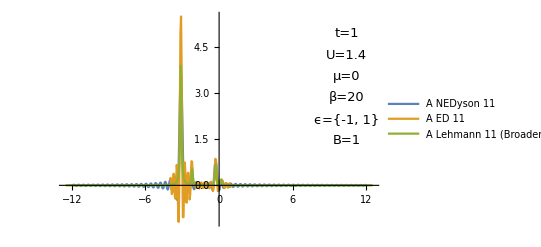
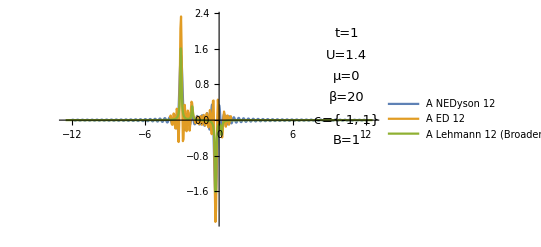
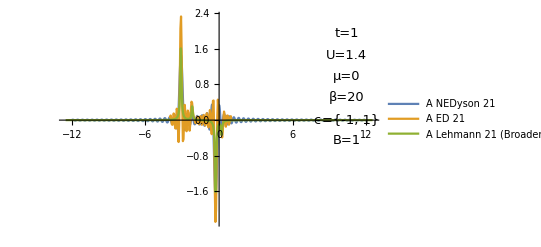
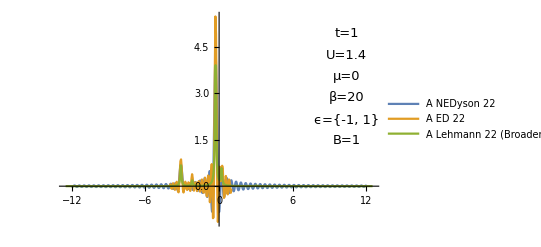

```mathematica
Aplots=ListPlot[
{Transpose[{Range[-Param[[4]],Param[[4]]+10^-10,Param[[5]]],ANEdysondata[[;;,(#[[1]]-1)*sites+#[[2]]]]}],Transpose[{wftlist,FTdata[[#[[1]],#[[2]],;;]]}],Transpose[{wlist,Lehmanndata[[#[[1]],#[[2]],;;]]}]},Joined->True,PlotRange->Full,Epilog->{Text[Style["t="<>ToString[t],13],Scaled[{0.9,0.9}]],Text[Style["U="<>ToString[U],13],Scaled[{0.9,0.8}]],Text[Style["μ="<>ToString[μ],13],Scaled[{0.9,0.7}]],Text[Style["β="<>ToString[β],13],Scaled[{0.9,0.6}]],Text[Style["ϵ="<>ToString[ϵ],13],Scaled[{0.9,0.5}]],Text[Style["B="<>ToString[B],13],Scaled[{0.9,0.4}]]},PlotLegends->{"A NEDyson "<>ToString[#[[1]]]<>ToString[#[[2]]],"A ED "<>ToString[#[[1]]]<>ToString[#[[2]]],"A Lehmann "<>ToString[#[[1]]]<>ToString[#[[2]]]"\n(Broadened)"}]&/@Flatten[Table[Table[{i,j},{j,1,sites}],{i,1,sites}],1]
```

```mathematica
Table[Table[Export["B"<>ToString[B]<>"U"<>ToString[U]<>"A"<>ToString[i]<>ToString[j]<>".eps",Aplots[[(i-1)*sites+j]]],{j,1,sites}],{i,1,sites}]
```

{{B1U1.4A11.eps,B1U1.4A12.eps},{B1U1.4A21.eps,B1U1.4A22.eps}}

## Junk Below here

```mathematica
wlist={1};
Timing[Table[Table[Function[{w},FTf1D[24,w,i,j]]/@wlist,{j,1,2sites,2}],{i,1,2sites,2}]]
```

{1}

{19.455,{{{-0.0560902},{0.0108044}},{{0.0108044},{-0.0838365}}}}

```mathematica
Timing[FTf1D[24,1,1,1]]
```

{4.62574,-0.0560902}

```mathematica
FTf1D[tmax_,w_,i_,j_]:=-1/Pi Im[Integrate[GRf1D[trel,i,j]Exp[I w trel],{trel,0,tmax}]];
```